## Attempt

## 0. edge

```mathematica
e=.7;g=10;
edge[x_]:=Max@{x-5,-6,-√3 x-10}
```

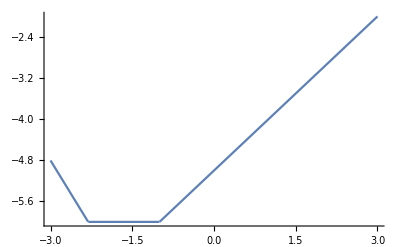

```mathematica
Plot[edge[x],{x,-3,3}]
```

## 1. Solve t

```mathematica
{xx,yy,vx,vy}={0,0,0,0};
```

```mathematica
tt=t/.Solve[{edge[xx+vx t]==yy+vy t-(g t^2)/2,t≥0},t]
```

{1}

```mathematica
Animate[Show[Plot[edge[x],{x,-3,3},PlotRange->{-7,1}],Graphics@Point@{xx+vx t,yy+vy t+-(g t^2)/2}],{t,0,1},AnimationRunning->False]
```

## 2. simple DSolve

```mathematica
k=10000;m=1;γ=10;g=10;
```

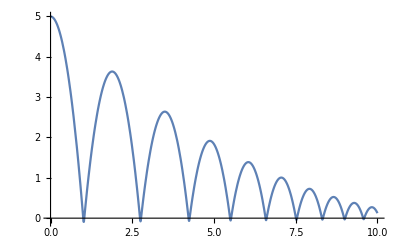

```mathematica
yyy[t_]=y[t]/.NDSolve[{m y''[t]==-g-Boole[y[t]<0](k y[t]+γ y'[t]),y[0]==5,y'[0]==0},y[t],{t,0,10}];
Plot[yyy[t],{t,0,10},PlotRange->All]
```

## 3. DSolve

```mathematica
edge'[x[t]]
```

Piecewise[{{-√3, x[t]<-4/(√3)}, {0, -4/(√3)<x[t]<-1}, {1, x[t]>-1}, {Indeterminate, True}}]

```mathematica
θ[x_]:=ArcTan[-√3 Boole[x<-4/(√3)]+Boole[x>-1]]
```

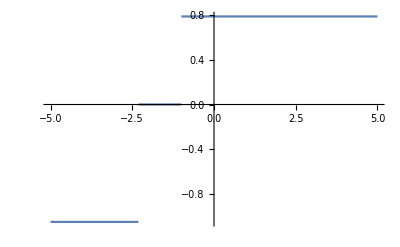

```mathematica
Plot[θ[x],{x,-5,5}]
```

```mathematica
ans=NDSolve[{
{m (y''Cos@θ-x''Sin@θ)==-g Cos@θ-Boole[y<edge@x](k (y-edge[x]) Cos@θ+γ(y' Cos@θ-x'Sin@θ)),
m (y''Sin@θ+x''Cos@θ)==-g Sin@θ}/.{x''->x''[t],y''->y''[t],x'->x'[t],y'->y'[t],x->x[t],y->y[t],θ->θ[x[t]]},y[0]==y'[0]==x'[0]==x[0]==0},{x[t],y[t]},{t,0,50}]
p[t_]={x[t],y[t]}/.First@ans;
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

```mathematica
Animate[Show[Plot[edge[x],{x,-10,5},PlotRange->{-7,0}],Graphics@Point@p[t]],{t,0,50},AnimationRate->1,AnimationRunning->False]
```

## 4. simplify

```mathematica
Solve[{vy2 Cos@θ-vx2 Sin@θ==-e(vy Cos@θ-vx Sin@θ),vy2 Sin@θ+vx2 Cos@θ==vy Sin@θ+vx Cos@θ},{vx2,vy2}]//FullSimplify
```

{{vx2→0.,vy2→0.}}

```mathematica
Clear[tt,xx,yy,vx,vy]
tt[0]=xx[0]=yy[0]=vx[0]=vy[0]=0;
tt[n_]:=tt[n]=Max@Append[Values@Quiet@NSolve[{edge[xx[n-1]+vx[n-1] t]==yy[n-1]+vy[n-1] t-(g t^2)/2,t>.00001},t],0]
xx[n_]:=xx[n]=xx[n-1]+vx[n-1]tt[n]
yy[n_]:=yy[n]=yy[n-1]+vy[n-1] tt[n]-(g tt[n]^2)/2(*edge@xx[n]*)
vx[n_]:=vx[n]=1/2 (vx-e vx+(1+e) vx Cos[2 θ]+(1+e) vy Sin[2 θ])/.{θ->θ@xx[n],vx->vx[n-1],vy->vy[n-1]-g tt[n]}
vy[n_]:=vy[n]=1/2 (-vy (-1+e+(1+e) Cos[2 θ])+(1+e) vx Sin[2 θ])/.{θ->θ@xx[n],vx->vx[n-1],vy->vy[n-1]-g tt[n]}
```

```mathematica
Array[tt,10,0]
```

{0,1.,0.283452,0.413212,0.825393,0.500115,0.481189,0.515527,0.476469,0.289576}

```mathematica
p[t_]=Module[{},at=Echo@Accumulate@Array[tt,#+1,0];Piecewise[Table[{{xx[n-1]+vx[n-1] t,yy[n-1]+vy[n-1] t+-(g t^2)/2}/.t->t-at⟦n⟧,at⟦n⟧≤t<at⟦n+1⟧},{n,1,#}],{xx[#],yy[#]}]]&@50;
```

{0,1.,1.28345,1.69666,2.52206,3.02217,3.50336,4.01889,4.49536,4.78493,5.03004,5.20161,5.32171,5.3672,5.60731,5.78051,5.90175,5.98662,6.04603,6.08762,6.11672,6.1371,6.15137,6.16135,6.16834,6.17323,6.17666,6.17905,6.18073,6.18191,6.18273,6.1833,6.18371,6.18399,6.18419,6.18432,6.18442,6.18449,6.18454,6.18457,6.18459,6.18461,6.18462,6.18462,6.18462,6.18462,6.18462,6.18462,6.18462,6.18462,6.18462}

```mathematica
Animate[Show[Plot[edge[x],{x,-8,8},PlotRange->{-7,1}],Graphics@Point@p[t]],{t,0,7},AnimationRunning->False]
```

## 5. several balls

```mathematica
Clear[ta,tt,code,xx,yy,ϕ,vx,vy]
```

```mathematica
FullSimplify@Solve[{vx1+vx2==vvx1+vvx2,vy1+vy2==vvy1+vvy2,
vx1 Cos@ϕ+vy1 Sin@ϕ-vx2 Cos@ϕ-vy2 Sin@ϕ==-e(vvx1 Cos@ϕ+vvy1 Sin@ϕ-vvx2 Cos@ϕ-vvy2 Sin@ϕ),
vx1 Sin@ϕ-vy1 Cos@ϕ-vx2 Sin@ϕ+vy2 Cos@ϕ==vvx1 Sin@ϕ-vvy1 Cos@ϕ-vvx2 Sin@ϕ+vvy2 Cos@ϕ},{vx1,vx2,vy1,vy2}]
```

{{vx1→1. ((0.15 vvx1+0.85 vvx2) Cos[ϕ]^2+(-0.85 vvy1+0.85 vvy2) Cos[ϕ] Sin[ϕ]+1. vvx1 Sin[ϕ]^2),vx2→1. ((0.85 vvx1+0.15 vvx2) Cos[ϕ]^2+(0.85 vvy1-0.85 vvy2) Cos[ϕ] Sin[ϕ]+1. vvx2 Sin[ϕ]^2),vy1→1. (1. vvy1 Cos[ϕ]^2+(-0.85 vvx1+0.85 vvx2) Cos[ϕ] Sin[ϕ]+(0.15 vvy1+0.85 vvy2) Sin[ϕ]^2),vy2→1. (1. vvy2 Cos[ϕ]^2+(0.85 vvx1-0.85 vvx2) Cos[ϕ] Sin[ϕ]+(0.85 vvy1+0.15 vvy2) Sin[ϕ]^2)}}

```mathematica
dis2[{p1_,p2_}]:=Total@((p1-p2)^2)
tb[{b1_,b2_}]:=Min@{Values@NSolve[{dis2[{#1+#3 t,#2+#4 t}&@@@{b1,b2}]==4,t≥.000001},t],100}
```

```mathematica
Manipulate[tb@{{0,0,a,0},{5,0,1,b}},{a,0,10},{b,0,5}]
```

```mathematica
nb=2;tt[0]=0;e=.7;
{xx[0],yy[0]}={{10,0},{0,0}};
{vx[0],vy[0]}={{-1,2},{0,0}};
```

```mathematica
nb=3;e=.9;tt[0]=0;
{xx[0],yy[0]}={{0,10,3},{0,0,6}};
{vx[0],vy[0]}={{1,-1,0},{0,0,-1}};
```

```mathematica
nb=4;tt[0]=0;
{xx[0],yy[0]}={{-5,0,5,0},{0,-5,0,5}};
{vx[0],vy[0]}={{1,0,-1,0},{0,1,0,-1}};
```

```mathematica
Clear[ta,tt,code,xx,yy,ϕ,vx,vy]
nb=3;e=.9;tt[0]=0;
{xx[0],yy[0]}={{0,10,3},{0,0,6}};
{vx[0],vy[0]}={{1,-1,0},{0,0,-1}};
ta[n_]:=ta[n]=Keys@#->tb@Values@#&/@Permutations[Range@nb->Transpose@{xx[n-1],yy[n-1],vx[n-1],vy[n-1]}//Thread,{2}]
tt[n_]:=tt[n]=Min@Values@ta[n]
code[n_]:=code[n]=ta[n]⟦FirstPosition[ta[n],tt[n]]⟦1⟧,1⟧
xx[n_]:=xx[n]=xx[n-1]+vx[n-1]tt[n]
yy[n_]:=yy[n]=yy[n-1]+vy[n-1]tt[n]
ϕ[n_]:=ϕ[n]=ArcTan[(#1-#2&@@xx[n-1]⟦code[n]⟧)/2,(#1-#2&@@yy[n-1]⟦code[n]⟧)/2]
vx[n_]:=vx[n]=Module[{vvx1,vvx2,vvy1,vvy2,ϕ=ϕ[n]},{vvx1,vvx2}=vx[n-1]⟦code[n]⟧;{vvy1,vvy2}=vy[n-1]⟦code[n]⟧;
ReplacePart[vx[n-1],{code[n]⟦1⟧->1/2 ((vvx1-e vvx1+vvx2+e vvx2) Cos[ϕ]^2-(1+e) (vvy1-vvy2) Cos[ϕ] Sin[ϕ]+2 vvx1 Sin[ϕ]^2),
code[n]⟦2⟧->1/2 ((vvx1+e vvx1+vvx2-e vvx2) Cos[ϕ]^2+(1+e) (vvy1-vvy2) Cos[ϕ] Sin[ϕ]+2 vvx2 Sin[ϕ]^2)}]]
vy[n_]:=vy[n]=Module[{vvx1,vvx2,vvy1,vvy2,ϕ=ϕ[n]},{vvx1,vvx2}=vx[n-1]⟦code[n]⟧;{vvy1,vvy2}=vy[n-1]⟦code[n]⟧;
ReplacePart[vy[n-1],{code[n]⟦1⟧->1/2 (2 vvy1 Cos[ϕ]^2-(1+e) (vvx1-vvx2) Cos[ϕ] Sin[ϕ]+(vvy1-e vvy1+vvy2+e vvy2) Sin[ϕ]^2),
code[n]⟦2⟧->1/2 (2 vvy2 Cos[ϕ]^2+(1+e) (vvx1-vvx2) Cos[ϕ] Sin[ϕ]+(vvy1+e vvy1+vvy2-e vvy2) Sin[ϕ]^2)}]]
Array[tt,10]
Array[ϕ,10]
Grid/@{Array[vx,10],Array[vy,10]}
p[t_]=Module[{},at=Echo@Accumulate@Array[tt,#+1,0];Piecewise[Table[{Transpose@{xx[n-1]+vx[n-1] t,yy[n-1]+vy[n-1] t}/.t->t-at⟦n⟧,at⟦n⟧≤t<at⟦n+1⟧},{n,1,#}],{xx[#],yy[#]}]]&@30;
```

{4.,0.182847,100,100,100,100,100,100,100,100}

{π,-1.10715,3.14159,-2.42779,-1.63793,-1.34617,-0.917275,-0.708814,-0.408298,-0.235179}

{-0.9 | 0.9 | 0
-0.349 | 0.9 | -0.551
0.83755 | -0.28655 | -0.551
0.745494 | -0.194494 | -0.551
0.821689 | -0.270689 | -0.551
0.97752 | -0.42652 | -0.551
0.319813 | 0.231187 | -0.551
0.909114 | -0.358114 | -0.551
0.0155325 | 0.535467 | -0.551
0.724019 | -0.173019 | -0.551,0. | 0. | -1
-1.102 | 0. | 0.102
-1.102 | 1.4531×10^-16 | 0.102
-1.18173 | 0.0797347 | 0.102
-0.0485042 | -1.0535 | 0.102
-0.730532 | -0.371468 | 0.102
0.128345 | -1.23034 | 0.102
-0.376963 | -0.725037 | 0.102
0.00960879 | -1.11161 | 0.102
-0.160154 | -0.941846 | 0.102}

{0,4.,4.18285,104.183,204.183,304.183,404.183,504.183,604.183,704.183,804.183,904.183,1004.18,1104.18,1204.18,1304.18,1404.18,1504.18,1604.18,1704.18,1804.18,1904.18,2004.18,2104.18,2204.18,2304.18,2404.18,2504.18,2604.18,2704.18,2804.18}

```mathematica
Manipulate[{Graphics[Circle/@p[t],PlotRange->{{-15,12},{-10,12}},ImageSize->Large],Grid@D[p[u],u]/.u->t},{t,0,15}]
```

### modified error: θ=ArcTan[x,y]=ArcTan[y/x]

### existing problem:

#### collide meanwhile

#### too slow

```mathematica
sdis=FullSimplify@Flatten@Values@Solve[{dis2[{#1+#3 t,#2+#4 t}&@@@{{xx1,yy1,vx1,vy1},{xx2,yy2,vx2,vy2}}]==4},t]
```

{1/((vx1-vx2)^2+(vy1-vy2)^2)(-vx1 xx1+vx2 xx1+vx1 xx2-vx2 xx2-vy1 yy1+vy2 yy1-1/2 √(4 ((vx1-vx2) (xx1-xx2)+(vy1-vy2) (yy1-yy2))^2-4 ((vx1-vx2)^2+(vy1-vy2)^2) (-4+(xx1-xx2)^2+(yy1-yy2)^2))+vy1 yy2-vy2 yy2),1/((vx1-vx2)^2+(vy1-vy2)^2)(-vx1 xx1+vx2 xx1+vx1 xx2-vx2 xx2-vy1 yy1+vy2 yy1+1/2 √(4 ((vx1-vx2) (xx1-xx2)+(vy1-vy2) (yy1-yy2))^2-4 ((vx1-vx2)^2+(vy1-vy2)^2) (-4+(xx1-xx2)^2+(yy1-yy2)^2))+vy1 yy2-vy2 yy2)}

```mathematica
ctb=Compile[{xx1,yy1,vx1,vy1,xx2,yy2,vx2,vy2},Module[{a=-vx1 xx1+vx2 xx1+vx1 xx2-vx2 xx2-vy1 yy1+vy2 yy1+vy1 yy2-vy2 yy2,c=(vx1-vx2)^2+(vy1-vy2)^2,b=4 ((vx1-vx2) (xx1-xx2)+(vy1-vy2) (yy1-yy2))^2-4 ((vx1-vx2)^2+(vy1-vy2)^2) (-4+(xx1-xx2)^2+(yy1-yy2)^2),w1,w2},If[b≤0,100,w1=(a+√b/2)/c;w2=(a-√b/2)/c;If[w2>.00001,w2,If[w1>.0001,w1,100]]]]]
```

CompiledFunction[…]

```mathematica
Clear[ta,tt,code,xx,yy,ϕ,vx,vy]
nb=50;e=.9;tt[0]=0;
{xx[0],yy[0],vx[0],vy[0]}=RandomInteger[{-10,10},{4,nb}];
ta[n_]:=ta[n]=Keys@#->ctb@@Flatten[Values@#]&/@Permutations[Range@nb->Transpose@{xx[n-1],yy[n-1],vx[n-1],vy[n-1]}//Thread,{2}]
tt[n_]:=tt[n]=Min@Values@ta[n]
code[n_]:=code[n]=ta[n]⟦FirstPosition[ta[n],tt[n]]⟦1⟧,1⟧
xx[n_]:=xx[n]=xx[n-1]+vx[n-1]tt[n]
yy[n_]:=yy[n]=yy[n-1]+vy[n-1]tt[n]
ϕ[n_]:=ϕ[n]=ArcTan[(#1-#2&@@xx[n-1]⟦code[n]⟧)/2,(#1-#2&@@yy[n-1]⟦code[n]⟧)/2]
vx[n_]:=vx[n]=Module[{vvx1,vvx2,vvy1,vvy2,ϕ=ϕ[n]},{vvx1,vvx2}=vx[n-1]⟦code[n]⟧;{vvy1,vvy2}=vy[n-1]⟦code[n]⟧;
ReplacePart[vx[n-1],{code[n]⟦1⟧->1/2 ((vvx1-e vvx1+vvx2+e vvx2) Cos[ϕ]^2-(1+e) (vvy1-vvy2) Cos[ϕ] Sin[ϕ]+2 vvx1 Sin[ϕ]^2),
code[n]⟦2⟧->1/2 ((vvx1+e vvx1+vvx2-e vvx2) Cos[ϕ]^2+(1+e) (vvy1-vvy2) Cos[ϕ] Sin[ϕ]+2 vvx2 Sin[ϕ]^2)}]]
vy[n_]:=vy[n]=Module[{vvx1,vvx2,vvy1,vvy2,ϕ=ϕ[n]},{vvx1,vvx2}=vx[n-1]⟦code[n]⟧;{vvy1,vvy2}=vy[n-1]⟦code[n]⟧;
ReplacePart[vy[n-1],{code[n]⟦1⟧->1/2 (2 vvy1 Cos[ϕ]^2-(1+e) (vvx1-vvx2) Cos[ϕ] Sin[ϕ]+(vvy1-e vvy1+vvy2+e vvy2) Sin[ϕ]^2),
code[n]⟦2⟧->1/2 (2 vvy2 Cos[ϕ]^2+(1+e) (vvx1-vvx2) Cos[ϕ] Sin[ϕ]+(vvy1+e vvy1+vvy2-e vvy2) Sin[ϕ]^2)}]]
p[t_]=Module[{},at=Accumulate@Array[tt,#+1,0];Piecewise[Table[{Transpose@{xx[n-1]+vx[n-1] t,yy[n-1]+vy[n-1] t}/.t->t-at⟦n⟧,at⟦n⟧≤t<at⟦n+1⟧},{n,1,#}],{xx[#],yy[#]}]]&@50;
```

## 6. balls and edge

```mathematica
te[{xx_,yy_,vx_,vy_}]:=Min@{Values@Quiet@NSolve[{edge[xx+vx t]==yy+vy t-(g t^2)/2,t>.00001},t],100}
```

```mathematica
eedge[x_]:=Max[x-5-√2,-7,-√3 x-12]
```

```mathematica
n=1;
tt[1]
FirstCase[Flatten@{ta[n],ta2},(a_->tt[n]):>a]
```

0.0165301

{11,24}

```mathematica
Clear[ta,ta2,tt,code,xx,yy,ϕ,vx,vy]
nb=2;tt[0]=0;e=.9;
{xx[0],yy[0]}={{-3,0},{0,0}};
{vx[0],vy[0]}={{0,0},{0,0}};
ta[n_]:=ta[n]=Keys@#->ctb@@Flatten[Values@#]&/@Permutations[Range@nb->Transpose@{xx[n-1],yy[n-1],vx[n-1],vy[n-1]}//Thread,{2}]
ta2[n_]:=ta2[n]=Keys@#->te@Values@#&/@Thread[Range@nb->Transpose@{xx[n-1],yy[n-1],vx[n-1],vy[n-1]}]
tt[n_]:=tt[n]=Min[Values@ta[n],Values@ta2[n]]
code[n_]:=code[n]=FirstCase[Flatten@{ta[n],ta2[n]},(a_->tt[n]):>a]
xx[n_]:=xx[n]=xx[n-1]+vx[n-1]tt[n]
yy[n_]:=yy[n]=yy[n-1]+vy[n-1] tt[n]-(g tt[n]^2)/2(*edge@xx[n]*)

ϕ[n_]:=ϕ[n]=ArcTan[(#1-#2&@@xx[n-1]⟦code[n]⟧)/2,(#1-#2&@@yy[n-1]⟦code[n]⟧)/2]
vx[n_]:=vx[n]=If[MatchQ[code[n],_List],
Module[{vvx1,vvx2,vvy1,vvy2,ϕ=ϕ[n]},{vvx1,vvx2}=vx[n-1]⟦code[n]⟧;{vvy1,vvy2}=vy[n-1]⟦code[n]⟧-g tt[n];
ReplacePart[vx[n-1],{code[n]⟦1⟧->1/2 ((vvx1-e vvx1+vvx2+e vvx2) Cos[ϕ]^2-(1+e) (vvy1-vvy2) Cos[ϕ] Sin[ϕ]+2 vvx1 Sin[ϕ]^2),
code[n]⟦2⟧->1/2 ((vvx1+e vvx1+vvx2-e vvx2) Cos[ϕ]^2+(1+e) (vvy1-vvy2) Cos[ϕ] Sin[ϕ]+2 vvx2 Sin[ϕ]^2)}]],ReplacePart[vx[n-1],code[n]->1/2 (vx-e vx+(1+e) vx Cos[2 θ]+(1+e) vy Sin[2 θ])/.{θ->θ@xx[n]⟦code[n]⟧,vx->vx[n-1]⟦code[n]⟧,vy->vy[n-1]⟦code[n]⟧-g tt[n]}]]
vy[n_]:=vy[n]=If[MatchQ[code,_List],
Module[{vvx1,vvx2,vvy1,vvy2,ϕ=ϕ[n]},{vvx1,vvx2}=vx[n-1]⟦code[n]⟧;{vvy1,vvy2}=vy[n-1]⟦code[n]⟧-g tt[n];
ReplacePart[vy[n-1]-g tt[n],{code[n]⟦1⟧->1/2 (2 vvy1 Cos[ϕ]^2-(1+e) (vvx1-vvx2) Cos[ϕ] Sin[ϕ]+(vvy1-e vvy1+vvy2+e vvy2) Sin[ϕ]^2),
code[n]⟦2⟧->1/2 (2 vvy2 Cos[ϕ]^2+(1+e) (vvx1-vvx2) Cos[ϕ] Sin[ϕ]+(vvy1+e vvy1+vvy2-e vvy2) Sin[ϕ]^2)}]],ReplacePart[vy[n-1]-g tt[n],code[n]->1/2 (-vy (-1+e+(1+e) Cos[2 θ])+(1+e) vx Sin[2 θ])/.{θ->θ@xx[n]⟦code[n]⟧,vx->vx[n-1]⟦code[n]⟧,vy->vy[n-1]⟦code[n]⟧-g tt[n]}]]
Array[vy,10]
```

{{-5.14599,-9.80189},{-5.3441,-0.5},{-5.82531,-0.981206},{4.00022,-1.25399},{3.77975,6.87814},{3.3464,6.44479},{1.89516,7.86616},{-3.54769,5.00866},{-2.44466,3.40637},{2.65054,2.90598}}

```mathematica
p[t_]=Module[{},at=Echo@Accumulate@Array[tt,#+1,0];Piecewise[Table[{Transpose@{xx[n-1]+vx[n-1] t,yy[n-1]+vy[n-1] t-(g t^2)/2}/.t->t-at⟦n⟧,at⟦n⟧≤t<at⟦n+1⟧},{n,1,#}],Transpose@{xx[#],yy[#]}]]&@100;
```

{0,0.980189,1.,1.04812,1.0754,1.09745,1.14078,1.2859,1.83019,1.99042,2.04046,2.32005,2.38156,2.76092,3.1577,3.27646,3.51481,3.8362,3.98388,3.99979,4.1137,4.12635,4.15462,4.21491,4.38066,4.81387,5.28052,5.42642,5.44598,5.44683,5.47589,5.4812,5.48328,5.68368,5.69644,5.72875,5.79243,5.97426,6.13791,6.2852,6.28637,6.41775,6.53706,6.64443,6.74106,6.78147,6.78635,6.83952,7.11014,7.1362,7.17223,7.18132,7.18303,7.18812,7.20726,7.22806,7.48112,7.7412,7.75841,7.83519,7.84655,7.87309,7.90403,7.92472,8.04935,8.20307,8.26617,8.34508,8.41319,8.60151,8.75321,8.78984,8.85535,8.9236,8.9545,8.9676,9.00982,9.04208,9.10123,9.35518,9.3701,9.38906,9.39537,9.40811,9.43056,9.45927,9.54524,9.71745,9.73345,9.75204,9.77628,9.80543,9.81352,9.83158,9.8344,9.83499,9.83664,9.88271,9.9058,9.94732,9.953}

```mathematica
Manipulate[{Show[Plot[eedge[x],{x,-10,10},AspectRatio->1],Graphics[Circle/@p[t]],PlotRange->{{-15,12},{-10,12}},ImageSize->Large],Grid@D[p[u],u]/.u->t},{t,0,10}]
```

### more balls

```mathematica
Clear[ta,ta2,tt,code,xx,yy,ϕ,vx,vy]
nb=4;tt[0]=0;e=.9;
{xx[0],yy[0],vx[0],vy[0]}=RandomInteger[{-3,5},{4,nb}];
ta[n_]:=ta[n]=Keys@#->ctb@@Flatten[Values@#]&/@Permutations[Range@nb->Transpose@{xx[n-1],yy[n-1],vx[n-1],vy[n-1]}//Thread,{2}]
ta2[n_]:=ta2[n]=Keys@#->te@Values@#&/@Thread[Range@nb->Transpose@{xx[n-1],yy[n-1],vx[n-1],vy[n-1]}]
tt[n_]:=tt[n]=Min[Values@ta[n],Values@ta2[n]]
code[n_]:=code[n]=FirstCase[Flatten@{ta[n],ta2[n]},(a_->tt[n]):>a]
xx[n_]:=xx[n]=xx[n-1]+vx[n-1]tt[n]
yy[n_]:=yy[n]=yy[n-1]+vy[n-1] tt[n]-(g tt[n]^2)/2(*edge@xx[n]*)

ϕ[n_]:=ϕ[n]=ArcTan[(#1-#2&@@xx[n-1]⟦code[n]⟧)/2,(#1-#2&@@yy[n-1]⟦code[n]⟧)/2]
vx[n_]:=vx[n]=If[MatchQ[code[n],_List],
Module[{vvx1,vvx2,vvy1,vvy2,ϕ=ϕ[n]},{vvx1,vvx2}=vx[n-1]⟦code[n]⟧;{vvy1,vvy2}=vy[n-1]⟦code[n]⟧-g tt[n];
ReplacePart[vx[n-1],{code[n]⟦1⟧->1/2 ((vvx1-e vvx1+vvx2+e vvx2) Cos[ϕ]^2-(1+e) (vvy1-vvy2) Cos[ϕ] Sin[ϕ]+2 vvx1 Sin[ϕ]^2),
code[n]⟦2⟧->1/2 ((vvx1+e vvx1+vvx2-e vvx2) Cos[ϕ]^2+(1+e) (vvy1-vvy2) Cos[ϕ] Sin[ϕ]+2 vvx2 Sin[ϕ]^2)}]],ReplacePart[vx[n-1],code[n]->1/2 (vx-e vx+(1+e) vx Cos[2 θ]+(1+e) vy Sin[2 θ])/.{θ->θ@xx[n]⟦code[n]⟧,vx->vx[n-1]⟦code[n]⟧,vy->vy[n-1]⟦code[n]⟧-g tt[n]}]]
vy[n_]:=vy[n]=If[MatchQ[code,_List],
Module[{vvx1,vvx2,vvy1,vvy2,ϕ=ϕ[n]},{vvx1,vvx2}=vx[n-1]⟦code[n]⟧;{vvy1,vvy2}=vy[n-1]⟦code[n]⟧-g tt[n];
ReplacePart[vy[n-1]-g tt[n],{code[n]⟦1⟧->1/2 (2 vvy1 Cos[ϕ]^2-(1+e) (vvx1-vvx2) Cos[ϕ] Sin[ϕ]+(vvy1-e vvy1+vvy2+e vvy2) Sin[ϕ]^2),
code[n]⟦2⟧->1/2 (2 vvy2 Cos[ϕ]^2+(1+e) (vvx1-vvx2) Cos[ϕ] Sin[ϕ]+(vvy1+e vvy1+vvy2-e vvy2) Sin[ϕ]^2)}]],ReplacePart[vy[n-1]-g tt[n],code[n]->1/2 (-vy (-1+e+(1+e) Cos[2 θ])+(1+e) vx Sin[2 θ])/.{θ->θ@xx[n]⟦code[n]⟧,vx->vx[n-1]⟦code[n]⟧,vy->vy[n-1]⟦code[n]⟧-g tt[n]}]]
p[t_]=Module[{},at=Echo@Accumulate@Array[tt,#+1,0];Piecewise[Table[{Transpose@{xx[n-1]+vx[n-1] t,yy[n-1]+vy[n-1] t-(g t^2)/2}/.t->t-at⟦n⟧,at⟦n⟧≤t<at⟦n+1⟧},{n,1,#}],Transpose@{xx[#],yy[#]}]]&@100;
```

{0,0.588235,0.76619,1.,1.73618,1.84202,1.86726,1.88128,2.02925,2.18468,2.39622,2.53433,2.72649,4.44093,4.89197,5.76408,7.31053,8.56941,9.3383,9.56716,10.8192,11.3057,11.8117,12.8822,13.4538,113.454,213.454,313.454,413.454,513.454,613.454,713.454,813.454,913.454,1013.45,1113.45,1213.45,1313.45,1413.45,1513.45,1613.45,1713.45,1813.45,1913.45,2013.45,2113.45,2213.45,2313.45,2413.45,2513.45,2613.45,2713.45,2813.45,2913.45,3013.45,3113.45,3213.45,3313.45,3413.45,3513.45,3613.45,3713.45,3813.45,3913.45,4013.45,4113.45,4213.45,4313.45,4413.45,4513.45,4613.45,4713.45,4813.45,4913.45,5013.45,5113.45,5213.45,5313.45,5413.45,5513.45,5613.45,5713.45,5813.45,5913.45,6013.45,6113.45,6213.45,6313.45,6413.45,6513.45,6613.45,6713.45,6813.45,6913.45,7013.45,7113.45,7213.45,7313.45,7413.45,7513.45,7613.45}

## 7. WhenEvent

```mathematica
e=.9;g=10;
θ[x_]:=ArcTan[-√3 Boole[x<-4/(√3)]+Boole[x>-1]]
```

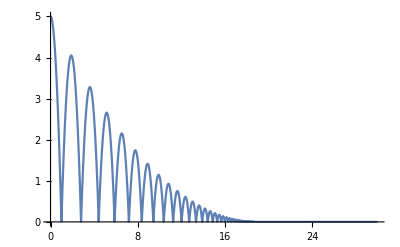

```mathematica
yyy[t_]=y[t]/.NDSolve[{y'''[t]==0,y[0]==5,y'[0]==0,y''[0]==-g,WhenEvent[y[t]==0,{y''[t],y'[t]}->If[y'[t]≥-1*^-4,{0,0},{-g,-e y'[t]}]]},y,{t,0,30}];
Plot[yyy[t],{t,0,30},PlotPoints->100]
```

```mathematica
ans=NDSolve[{
{y'''==0,x''==0,WhenEvent[y-edge[x]==0,{y'',y',x'}->If[y'Cos@θ-x'Sin@θ>-1*^-4,{0,0,0},{-g,1/2 (-y' (-1+e+(1+e) Cos[2 θ])+(1+e) x' Sin[2 θ]),1/2 (x'-e x'+(1+e) x' Cos[2 θ]+(1+e) y' Sin[2 θ])}],"DetectionMethod"->"DerivativeSign"]}/.{y'''->y'''[t],x''->x''[t],y''->y''[t],x'->x'[t],y'->y'[t],x->x[t],y->y[t],θ->θ[x[t]]},y''[0]==-g,y[0]==y'[0]==x'[0]==0,x[0]==1},{x[t],y[t]},{t,0,30}]
p[t_]={x[t],y[t]}/.ans;
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

```mathematica
Manipulate[Show[Graphics[Circle/@p[t],Axes->True],Plot[eedge[x],{x,-10,10}],PlotRange->{{-10,10},{-10,3}}],{t,0,30}]
```

```mathematica
nb=3;
part1=Table[{{y'''==0,x''==0,WhenEvent[y-edge[x]==0,
{y'',y',x'}->If[Abs[y'Cos@θ-x'Sin@θ]<1*^-6,{0,0,0},{-g,1/2 (-y' (-1+e+(1+e) Cos[2 θ])+(1+e) x' Sin[2 θ]),1/2 (x'-e x'+(1+e) x' Cos[2 θ]+(1+e) y' Sin[2 θ])}]]}/.{y'''->y'''[t],x''->x''[t],y''->y''[t],x'->x'[t],y'->y'[t],x->x[t],y->y[t],θ->θ[x[t]]},y''[0]==-g,x[0]==3-3i,y[0]==i-1,y'[0]==x'[0]==0}/.{x->x[i],y->y[i]},{i,nb}];
```

```mathematica
a2=First@NDSolve[part1,Table[{x[i][t],y[i][t]},{i,1,nb}],{t,0,30}]
p[t_]=Values@a2;
```

{{x[1][t],y[1][t]}→{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{x[2][t],y[2][t]}→{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{x[3][t],y[3][t]}→{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

```mathematica
part2=Table[WhenEvent[(x1-x2)^2+(y1-y2)^2-4<0,{ϕ=ArcTan[x1-x2,y1-y2],
{vx1,vx2,vy1,vy2}->{1/2 ((vx1-e vx1+vx2+e vx2) Cos[ϕ]^2-(1+e) (vy1-vy2) Cos[ϕ] Sin[ϕ]+2 vx1 Sin[ϕ]^2),1/2 ((vx1+e vx1+vx2-e vx2) Cos[ϕ]^2+(1+e) (vy1-vy2) Cos[ϕ] Sin[ϕ]+2 vx2 Sin[ϕ]^2),1/2 (2 vy1 Cos[ϕ]^2-(1+e) (vx1-vx2) Cos[ϕ] Sin[ϕ]+(vy1-e vy1+vy2+e vy2) Sin[ϕ]^2),1/2 (2 vy2 Cos[ϕ]^2+(1+e) (vx1-vx2) Cos[ϕ] Sin[ϕ]+(vy1+e vy1+vy2-e vy2) Sin[ϕ]^2)}}]/.{x1->x[i][t],x2->x[j][t],y1->y[i][t],y2->y[j][t],vx1->x[i]'[t],vx2->x[j]'[t],vy1->y[i]'[t],vy2->y[j]'[t]},{i,1,nb},{j,i+1,nb}];
```

```mathematica
a3=First@NDSolve[{part1,part2},Table[{x[i][t],y[i][t]},{i,nb}],{t,0,16}]
p[t_]=Values@a3;
```

{{x[1][t],y[1][t]}→{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{x[2][t],y[2][t]}→{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{x[3][t],y[3][t]}→{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

## force

```mathematica
fo[x_,y_,vx_,vy_]:=Boole[y<edge[x]](10000(edge[x]-y)Cos@θ[x]{-Sin@θ[x],Cos@θ[x]}-{vx,vy}10);
```

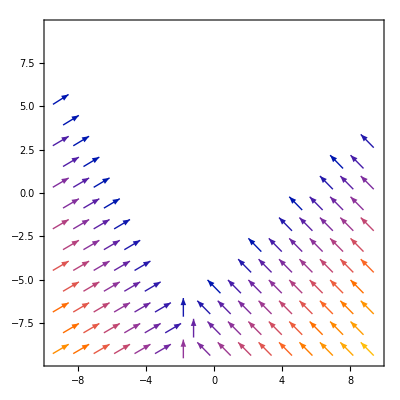

```mathematica
VectorPlot[fo[x,y,1,-3],{x,-9,9},{y,-9,9}]
```

```mathematica
ans=NDSolve[{{{x'',y''+g}==fo[x,y,x',y']}/.{x''->x''[t],x'->x'[t],y'->y'[t],y''->y''[t],x->x[t],y->y[t]},x[0]==x'[0]==y'[0]==0,y[0]==-1},{x[t],y[t]},{t,0,30}];
p[t_]={x[t],y[t]}/.ans
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

```mathematica
Plot[Total@Total@(p'[t]^2/2)+10Total[Last/@p[t]+9],{t,0,30},PlotRange->All]//Dynamic
```

```mathematica
ans=NDSolve[{{{x'',y''+g}==fo2[x,y,x',y']}/.{x''->x''[t],x'->x'[t],y'->y'[t],y''->y''[t],x->x[t],y->y[t]},x[0]==x'[0]==y'[0]==0,y[0]==5},{x[t],y[t]},{t,0,30}];
p[t_]={x[t],y[t]}/.ans
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

```mathematica
Manipulate[Show[Graphics[Circle/@p[t],Axes->True],Plot[eedge[x],{x,-10,10}],PlotRange->{{-10,10},{-10,10}}],{t,0,30}]
```

#### e = .8

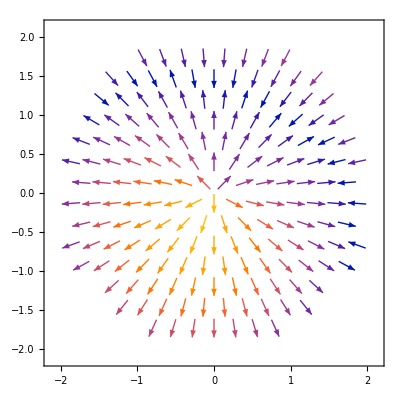

```mathematica
fo2[x_,y_,vx_,vy_]:=Boole[x^2+y^2<4](10(4-x^2-y^2)-{vx,vy}.Normalize@{x,y})Normalize@{x,y};
VectorPlot[fo2[x,y,10,20],{x,-2,2},{y,-2,2}]
```

```mathematica
nb=2;eq=Table[{x[j]''[t],y[j]''[t]}==fo[x[j][t],y[j][t],x[j]'[t],y[j]'[t]]+Sum[fo2[x[j][t]-x[i][t],y[j][t]-y[i][t],x[j]'[t]-x[i]'[t],y[j]'[t]-y[i]'[t]],{i,Drop[Range@nb,{j}]}],{j,nb}];
tj=Table[{x[0]==6-4i,y[0]==8,y'[0]==0,x'[0]==30-20i}/.{x->x[i],y->y[i]},{i,nb}];
```

```mathematica
nb=2;eq:=Table[{x[j]''[t],y[j]''[t]+g}==fo[x[j][t],y[j][t],x[j]'[t],y[j]'[t]]+Sum[fo2[x[j][t]-x[i][t],y[j][t]-y[i][t],x[j]'[t]-x[i]'[t],y[j]'[t]-y[i]'[t]],{i,Drop[Range@nb,{j}]}],{j,nb}];
tj:=Table[{x[0]==6-4i,y[0]==7,y'[0]==x'[0]==0}/.{x->x[i],y->y[i]},{i,nb}];
```

```mathematica
Timing[a4=First@NDSolve[{eq,tj},Table[{x[i][t],y[i][t]},{i,nb}],{t,0,30}]]
p[t_]=Values@a4;
```

{23.2031,{{x[1][t],y[1][t]}→{InterpolatingFunction[{{0., 30.}}, <>][t],InterpolatingFunction[{{0., 30.}}, <>][t]},{x[2][t],y[2][t]}→{InterpolatingFunction[{{0., 30.}}, <>][t],InterpolatingFunction[{{0., 30.}}, <>][t]}}}